## First we generate all graphs

We will generate an association containing all graphs.  The key of the graph is computed based on a base 4 representation of the upper half of the “adjacency matrix”.
The matrix itself is tri-valued since 0 means no edge, 1 means and edge and 2 mean they are the same vertex.
For each graph we keep

signature  : the "key"
matrix : the "adjancency matrix"
vertexsets : the "sets " of vertices where contracted vertices are in the same set
vertices : th evertices of the graph
edges : the edges of the graph
graph : a picture of the graph

```mathematica
baseGraphs5=GenAll[5];Length[baseGraphs5]
```

1895

## Now we calculate the relations

We calculate the relations between the graphs.  This is based on the deletion contraction rule.  It links 5 graphs together in a a=b+c relation (or a subtraction)

```mathematica
withRelations5=CompleteRelations[baseGraphs5];Length[withRelations5]
```

1895

For each graph we now add

links  : ids of graphs that are  linked to this graph
relations : a set of equations that involve the current graph.  This set can be empty.  The graph can be mentioned in the relations section of another graph

## Impose a colofour value for the 15 base graphs and propagate this to the others

```mathematica
Table[Labeled[withRelations5[k,"graph"],k],{k,Take[Keys[withRelations5],20]}]
```

{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-6,-Graphics-9,-Graphics-10,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-16,-Graphics-18,-Graphics-22,-Graphics-26,-Graphics-27,-Graphics-28,-Graphics-30,-Graphics-31,-Graphics-36}

```mathematica
{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-9,-Graphics-10,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-15,-Graphics-18,-Graphics-22,-Graphics-25,-Graphics-27,-Graphics-28,-Graphics-30,-Graphics-31,-Graphics-35}
```

{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-9,-Graphics-10,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-15,-Graphics-18,-Graphics-22,-Graphics-25,-Graphics-27,-Graphics-28,-Graphics-30,-Graphics-31,-Graphics-35}

We take a list of graphs as defined in https://en.wikipedia.org/wiki/Bell_number and give them an arbitrary value.

```mathematica
completeGraphs5=Select[Reverse[Keys[withRelations5]],CompleteGraphQ[withRelations5[#,"graph"]]&];Length[completeGraphs5]
```

52

```mathematica
baseGraphAxioma5=Block[{start=0},Table[start++;Symbol["x"<>ToString[k]]->PartitionToSymbol[withRelations5[k,"vertexsets"]],{k,completeGraphs5}]]
```

{x59048→v12345,x58288→v1234x5,x56770→v1235x4,x56012→v123x45,x56011→v123x4x5,x52232→v1245x3,x51478→v124x35,x51475→v124x3x5,x49972→v125x34,x49963→v125x3x4,x49220→v12x345,x49216→v12x34x5,x49210→v12x35x4,x49208→v12x3x45,x49207→v12x3x4x5,x39014→v1345x2,x38308→v134x25,x38281→v134x2x5,x36898→v135x24,x36817→v135x2x4,x36194→v13x245,x36166→v13x24x5,x36112→v13x25x4,x36086→v13x2x45,x36085→v13x2x4x5,x32684→v145x23,x32441→v145x2x3,x31984→v14x235,x31954→v14x23x5,x31738→v14x25x3,x31714→v14x2x35,x31711→v14x2x3x5,x30586→v15x234,x30496→v15x23x4,x30334→v15x24x3,x30262→v15x2x34,x30253→v15x2x3x4,x29888→v1x2345,x29857→v1x234x5,x29797→v1x235x4,x29768→v1x23x45,x29767→v1x23x4x5,x29633→v1x245x3,x29608→v1x24x35,x29605→v1x24x3x5,x29560→v1x25x34,x29551→v1x25x3x4,x29537→v1x2x345,x29533→v1x2x34x5,x29527→v1x2x35x4,x29525→v1x2x3x45,x29524→v1x2x3x4x5}

Now we get some lists of variables

```mathematica
allGraphVariables5=Table[Symbol["x"<> ToString[key]],{key,Keys[withRelations5]}];Length[allGraphVariables5]
```

1895

```mathematica
baseGraphAxioma5Vars=Sort[DeleteDuplicates[Flatten[Map[getAllVariables[#[[2]]]&,baseGraphAxioma5]]]];Length[baseGraphAxioma5Vars]
```

52

```mathematica
baseKeys5=Map[SymbolToKey[#[[1]]]&,baseGraphAxioma5]
```

{59048,58288,56770,56012,56011,52232,51478,51475,49972,49963,49220,49216,49210,49208,49207,39014,38308,38281,36898,36817,36194,36166,36112,36086,36085,32684,32441,31984,31954,31738,31714,31711,30586,30496,30334,30262,30253,29888,29857,29797,29768,29767,29633,29608,29605,29560,29551,29537,29533,29527,29525,29524}

```mathematica
Take[baseGraphAxioma5Vars,5]
```

{v12345,v1234x5,v1235x4,v123x45,v123x4x5}

```mathematica
{v123455,v12345x5,v12345x5,v1234x55,v1234x5x5}
```

{v123455,v12345x5,v12345x5,v1234x55,v1234x5x5}

We now take all relations.  Then we combined this with the base graph axioms.  This gives a huge expression list of 7507 equations

We are now in a position to assign the first colofour to each graph:

```mathematica
Monitor[Table[
withRelations5[key]["colofour"]=Simplify[Symbol["x"<>ToString[key]]/.baseGraphAxioma5],
{key,baseKeys5}
],key];
```

## Calculate the colortables

First we create the colortables, inventing variables on the fly if we need them.  Then we solve these variables and discover that once again we can get away with only the 52 base variables.
This procedure only works fior the b01... variables since we need 5 vertices for the current implementation

```mathematica
withColorTables5=withRelations5;
```

```mathematica
GenerateColorTable5[assocs_,key_]:=Block[
{mat=assocs[key]["matrix"], comb, colofour=assocs[key]["colofour"],newsym,value},

comb=Subsets[Range[5],{2}];
Table[
value=mat[[c[[1]],c[[2]]]];
If[value==2,
{colofour,0},
If[value==1,
{0,colofour},
newsym=Symbol["x"<>ToString[key]<>"y"<>ToString[c[[1]]]<>"z"<>ToString[c[[2]]]];
{newsym,colofour-newsym}
]
]
,{c,comb}
]
]
```

Example of one color table:

```mathematica
GenerateColorTable5[withColorTables5,2]
```

{{x2y1z2,-x2y1z2+Missing[KeyAbsent,colofour]},{x2y1z3,-x2y1z3+Missing[KeyAbsent,colofour]},{x2y1z4,-x2y1z4+Missing[KeyAbsent,colofour]},{x2y1z5,-x2y1z5+Missing[KeyAbsent,colofour]},{x2y2z3,-x2y2z3+Missing[KeyAbsent,colofour]},{x2y2z4,-x2y2z4+Missing[KeyAbsent,colofour]},{x2y2z5,-x2y2z5+Missing[KeyAbsent,colofour]},{x2y3z4,-x2y3z4+Missing[KeyAbsent,colofour]},{x2y3z5,-x2y3z5+Missing[KeyAbsent,colofour]},{Missing[KeyAbsent,colofour],0}}

First assign a basic colortable to each base graph

```mathematica
baseGraphKeys5=baseKeys5;
```

```mathematica
baseGraphAxioma5Vars
```

{v12345,v1234x5,v1235x4,v123x45,v123x4x5,v1245x3,v124x35,v124x3x5,v125x34,v125x3x4,v12x345,v12x34x5,v12x35x4,v12x3x45,v12x3x4x5,v1345x2,v134x25,v134x2x5,v135x24,v135x2x4,v13x245,v13x24x5,v13x25x4,v13x2x45,v13x2x4x5,v145x23,v145x2x3,v14x235,v14x23x5,v14x25x3,v14x2x35,v14x2x3x5,v15x234,v15x23x4,v15x24x3,v15x2x34,v15x2x3x4,v1x2345,v1x234x5,v1x235x4,v1x23x45,v1x23x4x5,v1x245x3,v1x24x35,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x345,v1x2x34x5,v1x2x35x4,v1x2x3x45,v1x2x3x4x5}

```mathematica
Monitor[Table[
withColorTables5[k]["colortable"]=GenerateColorTable5[withColorTables5,k]
,
{k,baseGraphKeys5}
],k];
```

```mathematica
Keys[withColorTables5[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links}

```mathematica
NoPrint[p__]:=TrueQ
```

Now we assign the other colortables by making sure their colofour formula is interpreted with the based color tables

```mathematica
TryComputeColourTable5[k_]:=Block[{result=Null,simp,left,r1,r2, done,current},
current=withColorTables5[k];
If[KeyExistsQ[current,"colortable"],
result=withColorTables5[k,"colortable"],
done=False;
Table[
If[!done,
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];
If[!KeyExistsQ[withColorTables5[r1],"colortable"],
withColorTables5[r1,"colortable"]=TryComputeColourTable5[r1],
];
If[!KeyExistsQ[withColorTables5[r2],"colortable"],
withColorTables5[r2,"colortable"]=TryComputeColourTable5[r2],

];
withColorTables5[k,"colortable"]=withColorTables5[r1,"colortable"]+withColorTables5[r2,"colortable"];
withColorTables5[k,"colofour"]=withColorTables5[r1,"colofour"]+withColorTables5[r2,"colofour"];
done=False
];
],
]
,{r,withColorTables5[k]["relations"]}
]
];
withColorTables5[k,"colortable"]
]
```

```mathematica
KeyExistsQ[withColorTables5[0],"colortable"]
```

False

```mathematica
Keys[withColorTables5[4782959]]
```

Keys::invrl: The argument Keys[Missing["KeyAbsent", 4782959]] is not a valid Association or a list of rules.

Keys[Missing[KeyAbsent,4782959]]

```mathematica
TryComputeColourTable5[0]
```

{{v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5,v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5},{v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5,v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5},{v12345+v1234x5+v1245x3+v124x35+v124x3x5+v1345x2+v134x25+v134x2x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5,v1235x4+v123x45+v123x4x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5},{v12345+v1235x4+v1245x3+v125x34+v125x3x4+v1345x2+v135x24+v135x2x4+v145x23+v145x2x3+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4,v1234x5+v123x45+v123x4x5+v124x35+v124x3x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v134x25+v134x2x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5},{v12345+v1234x5+v1235x4+v123x45+v123x4x5+v145x23+v14x235+v14x23x5+v15x234+v15x23x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5,v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x2x3+v14x25x3+v14x2x35+v14x2x3x5+v15x24x3+v15x2x34+v15x2x3x4+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5},{v12345+v1234x5+v1245x3+v124x35+v124x3x5+v135x24+v13x245+v13x24x5+v15x234+v15x24x3+v1x2345+v1x234x5+v1x245x3+v1x24x35+v1x24x3x5,v1235x4+v123x45+v123x4x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x2x4+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x235x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5},{v12345+v1235x4+v1245x3+v125x34+v125x3x4+v134x25+v13x245+v13x25x4+v14x235+v14x25x3+v1x2345+v1x235x4+v1x245x3+v1x25x34+v1x25x3x4,v1234x5+v123x45+v123x4x5+v124x35+v124x3x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x2x5+v135x24+v135x2x4+v13x24x5+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5},{v12345+v1234x5+v125x34+v12x345+v12x34x5+v1345x2+v134x25+v134x2x5+v15x234+v15x2x34+v1x2345+v1x234x5+v1x25x34+v1x2x345+v1x2x34x5,v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x3x4+v12x35x4+v12x3x45+v12x3x4x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x24x3+v15x2x3x4+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x45+v1x2x3x4x5},{v12345+v1235x4+v124x35+v12x345+v12x35x4+v1345x2+v135x24+v135x2x4+v14x235+v14x2x35+v1x2345+v1x235x4+v1x24x35+v1x2x345+v1x2x35x4,v1234x5+v123x45+v123x4x5+v1245x3+v124x3x5+v125x34+v125x3x4+v12x34x5+v12x3x45+v12x3x4x5+v134x25+v134x2x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5},{v12345+v123x45+v1245x3+v12x345+v12x3x45+v1345x2+v13x245+v13x2x45+v145x23+v145x2x3+v1x2345+v1x23x45+v1x245x3+v1x2x345+v1x2x3x45,v1234x5+v1235x4+v123x4x5+v124x35+v124x3x5+v125x34+v125x3x4+v12x34x5+v12x35x4+v12x3x4x5+v134x25+v134x2x5+v135x24+v135x2x4+v13x24x5+v13x25x4+v13x2x4x5+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x235x4+v1x23x4x5+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x4x5}}

Now collect all relation equations.  There are quite a few of them.

0

```mathematica
Monitor[Table[
withColorTables5[k]["colortable2"]=withColorTables5[k]["colortable"]
,
{k,Keys[withColorTables5]}
],k];
```

## Set “comp” and “compwhy” for graphs that can be embedded and are planar

```mathematica
withComp5=withColorTables5;
```

Start will all graphs GreaterEqual

```mathematica
Table[withComp5[k,"comp"]=GreaterEqual;withRelations5[k,"comp"]="No IH";k,{k,Keys[withComp5]}]//Length
```

1895

```mathematica
CosyPrint5[key_]:=With[
{current=withComp5[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{100,100}]
}
],Style[
{If[KeyExistsQ[current,"colofour"],
current["signature"]->TraditionalForm[current["colofour"]],
current["signature"]
],ChromaticPolynomial[current["graph"],4]/24},First[Select[{{"Equal",Blue},{"GreaterEqual",Red},{"Greater",Darker[Green]}},#[[1]]==ToString[current["comp"]]&]]]]]
]
```

```mathematica
ColofourPrint5[key_]:=With[
{current=withComp5[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{70,70}]
}
],
{Style[current["signature"],First[Select[{{"Equal",Blue},{"GreaterEqual",Red},{"Greater",Darker[Green]}},#[[1]]==ToString[current["comp"]]&]]]->TraditionalForm[current["colofour"]],ChromaticPolynomial[current["graph"],4]/24}]]]
```

```mathematica
MayBeReassign[key_,current_,left_,right_]:=Block[
{currentS=ToString[current],
leftS=ToString[left],
rightS=ToString[right],
 result=current},
(*Print[currentS,"  ", leftS, "  ", rightS];*)
If[currentS=="GreaterEqual",
If[leftS=="Greater"||rightS=="Greater",
result=Greater;
]
];
result
]
```

```mathematica
RecalculateComp5[k_,depth_,maxdepth_]:=Block[{result=Null,simp,left,r1,r2, current},
current=withComp5[k];
If[depth<maxdepth && ! current["marked"],
withComp5[k,"marked"]=True;
markCount++;
Table[
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];


withComp5[r1,"parents"]=Append[withComp5[r1,"parents"],k];
withComp5[r2,"parents"]=Append[withComp5[r2,"parents"],k];
withComp5[k,"children"]=Append[withComp5[k,"children"],{r1,r2}];

RecalculateComp5[r1,depth+1,maxdepth];
RecalculateComp5[r2,depth+1,maxdepth];
withComp5[k,"comp"]= MayBeReassign[k,withComp5[k,"comp"], withComp5[r1,"comp"],withComp5[r2,"comp"]]
];
]
,{r,withComp5[k]["relations"]}
];
];withComp5[k,"comp"]
]
```

```mathematica
Table[withComp5[k,"marked"]=False;withComp5[k,"parents"]={};withComp5[k,"children"]={};k,{k,Keys[withComp5]}];markCount=0
```

0

```mathematica
IsPlanarSet[set_,total_]:=Block[{result,sot=set-1,breaks=0,i,previous},
If[Length[set]==1,
result=True,
For[i=2,i≤Length[sot],i++,
If[Mod[sot[[i-1]]+1,total]≠Mod[sot[[i]],total],
breaks++;
]
];
If[Mod[sot[[Length[sot]]]+1,total]≠Mod[sot[[1]],total],
breaks++;
];
result=breaks<2;
];
result
]
```

```mathematica
IsPlanarContraction[assoc_,key_]:=Block[{total},
total=Length[Flatten[assoc[key,"vertexsets"]]];
Fold[And,Table[IsPlanarSet[s,total],{s,assoc[key,"vertexsets"]}]]
];
```

```mathematica
Table[If[
IsPlanarContraction[withComp5,k],
withComp5[k,"comp"]=Greater;
withComp5[k,"compwhy"]="Planar contraction";
1,
0]
,{k,baseKeys5}]
```

{1,1,1,1,1,1,0,0,1,1,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,1,1,1,1,0,1,1,0,0,0,0,0,1,1,0,1,1}

```mathematica
Table[withComp5[k,"comp"]=Equal;withComp5[k,"compwhy"]="Contains K Five";k,{k,Select[baseKeys5,!PlanarGraphQ[withComp5[#,"graph"]]&]}]//Length
```

1

```mathematica
15
```

15

```mathematica
Monitor[
Table[If[
PlanarGraphQ[EmbedGraph5[withComp5,key]],
Print[key, " is planar and follows IH "];
withComp5[key]["compwhy"]="Embedding is planar and follows IH";withComp5[key]["comp"]=Greater;
1,
0
],{key,Keys[withComp5]}],
key]//Total
```

0 is planar and follows IH

1 is planar and follows IH

2 is planar and follows IH

3 is planar and follows IH

4 is planar and follows IH

6 is planar and follows IH

9 is planar and follows IH

10 is planar and follows IH

12 is planar and follows IH

13 is planar and follows IH

14 is planar and follows IH

16 is planar and follows IH

18 is planar and follows IH

22 is planar and follows IH

26 is planar and follows IH

27 is planar and follows IH

28 is planar and follows IH

30 is planar and follows IH

31 is planar and follows IH

36 is planar and follows IH

37 is planar and follows IH

39 is planar and follows IH

40 is planar and follows IH

45 is planar and follows IH

49 is planar and follows IH

54 is planar and follows IH

63 is planar and follows IH

72 is planar and follows IH

81 is planar and follows IH

82 is planar and follows IH

90 is planar and follows IH

91 is planar and follows IH

108 is planar and follows IH

109 is planar and follows IH

110 is planar and follows IH

117 is planar and follows IH

118 is planar and follows IH

122 is planar and follows IH

136 is planar and follows IH

145 is planar and follows IH

162 is planar and follows IH

190 is planar and follows IH

218 is planar and follows IH

243 is planar and follows IH

244 is planar and follows IH

245 is planar and follows IH

246 is planar and follows IH

247 is planar and follows IH

252 is planar and follows IH

253 is planar and follows IH

255 is planar and follows IH

256 is planar and follows IH

257 is planar and follows IH

270 is planar and follows IH

271 is planar and follows IH

273 is planar and follows IH

274 is planar and follows IH

276 is planar and follows IH

279 is planar and follows IH

280 is planar and follows IH

282 is planar and follows IH

283 is planar and follows IH

286 is planar and follows IH

300 is planar and follows IH

309 is planar and follows IH

324 is planar and follows IH

325 is planar and follows IH

333 is planar and follows IH

334 is planar and follows IH

342 is planar and follows IH

346 is planar and follows IH

351 is planar and follows IH

352 is planar and follows IH

353 is planar and follows IH

360 is planar and follows IH

361 is planar and follows IH

365 is planar and follows IH

369 is planar and follows IH

373 is planar and follows IH

377 is planar and follows IH

382 is planar and follows IH

391 is planar and follows IH

400 is planar and follows IH

414 is planar and follows IH

442 is planar and follows IH

473 is planar and follows IH

486 is planar and follows IH

487 is planar and follows IH

488 is planar and follows IH

516 is planar and follows IH

517 is planar and follows IH

546 is planar and follows IH

576 is planar and follows IH

577 is planar and follows IH

606 is planar and follows IH

607 is planar and follows IH

608 is planar and follows IH

637 is planar and follows IH

666 is planar and follows IH

697 is planar and follows IH

728 is planar and follows IH

729 is planar and follows IH

730 is planar and follows IH

732 is planar and follows IH

733 is planar and follows IH

738 is planar and follows IH

739 is planar and follows IH

741 is planar and follows IH

742 is planar and follows IH

747 is planar and follows IH

751 is planar and follows IH

756 is planar and follows IH

757 is planar and follows IH

759 is planar and follows IH

760 is planar and follows IH

765 is planar and follows IH

766 is planar and follows IH

768 is planar and follows IH

769 is planar and follows IH

774 is planar and follows IH

778 is planar and follows IH

810 is planar and follows IH

811 is planar and follows IH

819 is planar and follows IH

820 is planar and follows IH

837 is planar and follows IH

838 is planar and follows IH

846 is planar and follows IH

847 is planar and follows IH

891 is planar and follows IH

919 is planar and follows IH

972 is planar and follows IH

973 is planar and follows IH

975 is planar and follows IH

976 is planar and follows IH

981 is planar and follows IH

982 is planar and follows IH

984 is planar and follows IH

985 is planar and follows IH

999 is planar and follows IH

1000 is planar and follows IH

1002 is planar and follows IH

1003 is planar and follows IH

1008 is planar and follows IH

1009 is planar and follows IH

1011 is planar and follows IH

1012 is planar and follows IH

1053 is planar and follows IH

1054 is planar and follows IH

1062 is planar and follows IH

1063 is planar and follows IH

1071 is planar and follows IH

1075 is planar and follows IH

1080 is planar and follows IH

1081 is planar and follows IH

1089 is planar and follows IH

1090 is planar and follows IH

1098 is planar and follows IH

1102 is planar and follows IH

1143 is planar and follows IH

1171 is planar and follows IH

1215 is planar and follows IH

1216 is planar and follows IH

1245 is planar and follows IH

1246 is planar and follows IH

1305 is planar and follows IH

1306 is planar and follows IH

1335 is planar and follows IH

1336 is planar and follows IH

1395 is planar and follows IH

1426 is planar and follows IH

1458 is planar and follows IH

1467 is planar and follows IH

1476 is planar and follows IH

1539 is planar and follows IH

1548 is planar and follows IH

1620 is planar and follows IH

1701 is planar and follows IH

1710 is planar and follows IH

1782 is planar and follows IH

1791 is planar and follows IH

1800 is planar and follows IH

1872 is planar and follows IH

1944 is planar and follows IH

2034 is planar and follows IH

2124 is planar and follows IH

2187 is planar and follows IH

2188 is planar and follows IH

2196 is planar and follows IH

2197 is planar and follows IH

2268 is planar and follows IH

2269 is planar and follows IH

2277 is planar and follows IH

2278 is planar and follows IH

2430 is planar and follows IH

2431 is planar and follows IH

2439 is planar and follows IH

2440 is planar and follows IH

2511 is planar and follows IH

2512 is planar and follows IH

2520 is planar and follows IH

2521 is planar and follows IH

2673 is planar and follows IH

2674 is planar and follows IH

2763 is planar and follows IH

2764 is planar and follows IH

2916 is planar and follows IH

2917 is planar and follows IH

2918 is planar and follows IH

2925 is planar and follows IH

2926 is planar and follows IH

2930 is planar and follows IH

2997 is planar and follows IH

2998 is planar and follows IH

3006 is planar and follows IH

3007 is planar and follows IH

3026 is planar and follows IH

3038 is planar and follows IH

3159 is planar and follows IH

3160 is planar and follows IH

3161 is planar and follows IH

3168 is planar and follows IH

3169 is planar and follows IH

3173 is planar and follows IH

3240 is planar and follows IH

3241 is planar and follows IH

3249 is planar and follows IH

3250 is planar and follows IH

3269 is planar and follows IH

3281 is planar and follows IH

3402 is planar and follows IH

3403 is planar and follows IH

3404 is planar and follows IH

3492 is planar and follows IH

3493 is planar and follows IH

3524 is planar and follows IH

3646 is planar and follows IH

3655 is planar and follows IH

3727 is planar and follows IH

3736 is planar and follows IH

3889 is planar and follows IH

3898 is planar and follows IH

3970 is planar and follows IH

3979 is planar and follows IH

4132 is planar and follows IH

4222 is planar and follows IH

4374 is planar and follows IH

4617 is planar and follows IH

4860 is planar and follows IH

5104 is planar and follows IH

5347 is planar and follows IH

5590 is planar and follows IH

5834 is planar and follows IH

6077 is planar and follows IH

6320 is planar and follows IH

6561 is planar and follows IH

6562 is planar and follows IH

6563 is planar and follows IH

6564 is planar and follows IH

6565 is planar and follows IH

6570 is planar and follows IH

6571 is planar and follows IH

6573 is planar and follows IH

6574 is planar and follows IH

6575 is planar and follows IH

6804 is planar and follows IH

6805 is planar and follows IH

6806 is planar and follows IH

6807 is planar and follows IH

6808 is planar and follows IH

6813 is planar and follows IH

6814 is planar and follows IH

6816 is planar and follows IH

6817 is planar and follows IH

6818 is planar and follows IH

7290 is planar and follows IH

7291 is planar and follows IH

7293 is planar and follows IH

7294 is planar and follows IH

7296 is planar and follows IH

7299 is planar and follows IH

7300 is planar and follows IH

7302 is planar and follows IH

7303 is planar and follows IH

7306 is planar and follows IH

7533 is planar and follows IH

7534 is planar and follows IH

7536 is planar and follows IH

7537 is planar and follows IH

7542 is planar and follows IH

7543 is planar and follows IH

7545 is planar and follows IH

7546 is planar and follows IH

7566 is planar and follows IH

7576 is planar and follows IH

8022 is planar and follows IH

8031 is planar and follows IH

8265 is planar and follows IH

8274 is planar and follows IH

8748 is planar and follows IH

8749 is planar and follows IH

8757 is planar and follows IH

8758 is planar and follows IH

8766 is planar and follows IH

8770 is planar and follows IH

8991 is planar and follows IH

8992 is planar and follows IH

9000 is planar and follows IH

9001 is planar and follows IH

9090 is planar and follows IH

9094 is planar and follows IH

9477 is planar and follows IH

9478 is planar and follows IH

9479 is planar and follows IH

9486 is planar and follows IH

9487 is planar and follows IH

9491 is planar and follows IH

9495 is planar and follows IH

9499 is planar and follows IH

9503 is planar and follows IH

9720 is planar and follows IH

9721 is planar and follows IH

9722 is planar and follows IH

9729 is planar and follows IH

9730 is planar and follows IH

9734 is planar and follows IH

9819 is planar and follows IH

9823 is planar and follows IH

9854 is planar and follows IH

10210 is planar and follows IH

10219 is planar and follows IH

10228 is planar and follows IH

10453 is planar and follows IH

10462 is planar and follows IH

10552 is planar and follows IH

10944 is planar and follows IH

11187 is planar and follows IH

11674 is planar and follows IH

11917 is planar and follows IH

12407 is planar and follows IH

12650 is planar and follows IH

13122 is planar and follows IH

13123 is planar and follows IH

13124 is planar and follows IH

13854 is planar and follows IH

13855 is planar and follows IH

14586 is planar and follows IH

15318 is planar and follows IH

15319 is planar and follows IH

16050 is planar and follows IH

16051 is planar and follows IH

16052 is planar and follows IH

16783 is planar and follows IH

17514 is planar and follows IH

18247 is planar and follows IH

18980 is planar and follows IH

19683 is planar and follows IH

19684 is planar and follows IH

19685 is planar and follows IH

19686 is planar and follows IH

19687 is planar and follows IH

19689 is planar and follows IH

19692 is planar and follows IH

19693 is planar and follows IH

19695 is planar and follows IH

19696 is planar and follows IH

19697 is planar and follows IH

19699 is planar and follows IH

19701 is planar and follows IH

19705 is planar and follows IH

19709 is planar and follows IH

19710 is planar and follows IH

19711 is planar and follows IH

19713 is planar and follows IH

19714 is planar and follows IH

19719 is planar and follows IH

19720 is planar and follows IH

19722 is planar and follows IH

19723 is planar and follows IH

19728 is planar and follows IH

19732 is planar and follows IH

19764 is planar and follows IH

19765 is planar and follows IH

19773 is planar and follows IH

19774 is planar and follows IH

19791 is planar and follows IH

19792 is planar and follows IH

19793 is planar and follows IH

19800 is planar and follows IH

19801 is planar and follows IH

19805 is planar and follows IH

19926 is planar and follows IH

19927 is planar and follows IH

19928 is planar and follows IH

19929 is planar and follows IH

19930 is planar and follows IH

19935 is planar and follows IH

19936 is planar and follows IH

19938 is planar and follows IH

19939 is planar and follows IH

19940 is planar and follows IH

19953 is planar and follows IH

19954 is planar and follows IH

19956 is planar and follows IH

19957 is planar and follows IH

19959 is planar and follows IH

19962 is planar and follows IH

19963 is planar and follows IH

19965 is planar and follows IH

19966 is planar and follows IH

19969 is planar and follows IH

20007 is planar and follows IH

20008 is planar and follows IH

20016 is planar and follows IH

20017 is planar and follows IH

20025 is planar and follows IH

20029 is planar and follows IH

20034 is planar and follows IH

20035 is planar and follows IH

20036 is planar and follows IH

20043 is planar and follows IH

20044 is planar and follows IH

20048 is planar and follows IH

20052 is planar and follows IH

20056 is planar and follows IH

20060 is planar and follows IH

20412 is planar and follows IH

20413 is planar and follows IH

20415 is planar and follows IH

20416 is planar and follows IH

20421 is planar and follows IH

20422 is planar and follows IH

20424 is planar and follows IH

20425 is planar and follows IH

20430 is planar and follows IH

20434 is planar and follows IH

20439 is planar and follows IH

20440 is planar and follows IH

20442 is planar and follows IH

20443 is planar and follows IH

20448 is planar and follows IH

20449 is planar and follows IH

20451 is planar and follows IH

20452 is planar and follows IH

20457 is planar and follows IH

20461 is planar and follows IH

20466 is planar and follows IH

20475 is planar and follows IH

20484 is planar and follows IH

20493 is planar and follows IH

20494 is planar and follows IH

20502 is planar and follows IH

20503 is planar and follows IH

20520 is planar and follows IH

20521 is planar and follows IH

20529 is planar and follows IH

20530 is planar and follows IH

20548 is planar and follows IH

20557 is planar and follows IH

20655 is planar and follows IH

20656 is planar and follows IH

20658 is planar and follows IH

20659 is planar and follows IH

20664 is planar and follows IH

20665 is planar and follows IH

20667 is planar and follows IH

20668 is planar and follows IH

20682 is planar and follows IH

20683 is planar and follows IH

20685 is planar and follows IH

20686 is planar and follows IH

20691 is planar and follows IH

20692 is planar and follows IH

20694 is planar and follows IH

20695 is planar and follows IH

20712 is planar and follows IH

20721 is planar and follows IH

20736 is planar and follows IH

20737 is planar and follows IH

20745 is planar and follows IH

20746 is planar and follows IH

20754 is planar and follows IH

20758 is planar and follows IH

20763 is planar and follows IH

20764 is planar and follows IH

20772 is planar and follows IH

20773 is planar and follows IH

20781 is planar and follows IH

20785 is planar and follows IH

20794 is planar and follows IH

20803 is planar and follows IH

20812 is planar and follows IH

21168 is planar and follows IH

21177 is planar and follows IH

21186 is planar and follows IH

21249 is planar and follows IH

21258 is planar and follows IH

21411 is planar and follows IH

21420 is planar and follows IH

21492 is planar and follows IH

21501 is planar and follows IH

21510 is planar and follows IH

21870 is planar and follows IH

21871 is planar and follows IH

21879 is planar and follows IH

21880 is planar and follows IH

21951 is planar and follows IH

21952 is planar and follows IH

21960 is planar and follows IH

21961 is planar and follows IH

22032 is planar and follows IH

22060 is planar and follows IH

22113 is planar and follows IH

22114 is planar and follows IH

22122 is planar and follows IH

22123 is planar and follows IH

22194 is planar and follows IH

22195 is planar and follows IH

22203 is planar and follows IH

22204 is planar and follows IH

22284 is planar and follows IH

22312 is planar and follows IH

22599 is planar and follows IH

22600 is planar and follows IH

22601 is planar and follows IH

22608 is planar and follows IH

22609 is planar and follows IH

22613 is planar and follows IH

22680 is planar and follows IH

22681 is planar and follows IH

22689 is planar and follows IH

22690 is planar and follows IH

22709 is planar and follows IH

22721 is planar and follows IH

22761 is planar and follows IH

22789 is planar and follows IH

22817 is planar and follows IH

22842 is planar and follows IH

22843 is planar and follows IH

22844 is planar and follows IH

22851 is planar and follows IH

22852 is planar and follows IH

22856 is planar and follows IH

22923 is planar and follows IH

22924 is planar and follows IH

22932 is planar and follows IH

22933 is planar and follows IH

22952 is planar and follows IH

22964 is planar and follows IH

23013 is planar and follows IH

23041 is planar and follows IH

23072 is planar and follows IH

23356 is planar and follows IH

23365 is planar and follows IH

23437 is planar and follows IH

23446 is planar and follows IH

23518 is planar and follows IH

23599 is planar and follows IH

23608 is planar and follows IH

23680 is planar and follows IH

23689 is planar and follows IH

23770 is planar and follows IH

24138 is planar and follows IH

24381 is planar and follows IH

24868 is planar and follows IH

25111 is planar and follows IH

25625 is planar and follows IH

25868 is planar and follows IH

26244 is planar and follows IH

26245 is planar and follows IH

26246 is planar and follows IH

26247 is planar and follows IH

26248 is planar and follows IH

26253 is planar and follows IH

26254 is planar and follows IH

26256 is planar and follows IH

26257 is planar and follows IH

26258 is planar and follows IH

26487 is planar and follows IH

26488 is planar and follows IH

26489 is planar and follows IH

26490 is planar and follows IH

26491 is planar and follows IH

26496 is planar and follows IH

26497 is planar and follows IH

26499 is planar and follows IH

26500 is planar and follows IH

26501 is planar and follows IH

26730 is planar and follows IH

26731 is planar and follows IH

26732 is planar and follows IH

26760 is planar and follows IH

26761 is planar and follows IH

26820 is planar and follows IH

26821 is planar and follows IH

26850 is planar and follows IH

26851 is planar and follows IH

26852 is planar and follows IH

26973 is planar and follows IH

26974 is planar and follows IH

26976 is planar and follows IH

26977 is planar and follows IH

26979 is planar and follows IH

26982 is planar and follows IH

26983 is planar and follows IH

26985 is planar and follows IH

26986 is planar and follows IH

26989 is planar and follows IH

27216 is planar and follows IH

27217 is planar and follows IH

27219 is planar and follows IH

27220 is planar and follows IH

27225 is planar and follows IH

27226 is planar and follows IH

27228 is planar and follows IH

27229 is planar and follows IH

27249 is planar and follows IH

27259 is planar and follows IH

27459 is planar and follows IH

27460 is planar and follows IH

27489 is planar and follows IH

27490 is planar and follows IH

27519 is planar and follows IH

27549 is planar and follows IH

27550 is planar and follows IH

27579 is planar and follows IH

27580 is planar and follows IH

27610 is planar and follows IH

27732 is planar and follows IH

27741 is planar and follows IH

27975 is planar and follows IH

27984 is planar and follows IH

28218 is planar and follows IH

28308 is planar and follows IH

28431 is planar and follows IH

28432 is planar and follows IH

28440 is planar and follows IH

28441 is planar and follows IH

28449 is planar and follows IH

28453 is planar and follows IH

28674 is planar and follows IH

28675 is planar and follows IH

28683 is planar and follows IH

28684 is planar and follows IH

28773 is planar and follows IH

28777 is planar and follows IH

28917 is planar and follows IH

28918 is planar and follows IH

29007 is planar and follows IH

29008 is planar and follows IH

29097 is planar and follows IH

29128 is planar and follows IH

29160 is planar and follows IH

29161 is planar and follows IH

29162 is planar and follows IH

29169 is planar and follows IH

29170 is planar and follows IH

29174 is planar and follows IH

29178 is planar and follows IH

29182 is planar and follows IH

29186 is planar and follows IH

29403 is planar and follows IH

29404 is planar and follows IH

29405 is planar and follows IH

29412 is planar and follows IH

29413 is planar and follows IH

29417 is planar and follows IH

29502 is planar and follows IH

29506 is planar and follows IH

29537 is planar and follows IH

29646 is planar and follows IH

29647 is planar and follows IH

29648 is planar and follows IH

29736 is planar and follows IH

29737 is planar and follows IH

29768 is planar and follows IH

29826 is planar and follows IH

29857 is planar and follows IH

29888 is planar and follows IH

29920 is planar and follows IH

29929 is planar and follows IH

29938 is planar and follows IH

30163 is planar and follows IH

30172 is planar and follows IH

30262 is planar and follows IH

30406 is planar and follows IH

30496 is planar and follows IH

30586 is planar and follows IH

30708 is planar and follows IH

30951 is planar and follows IH

31194 is planar and follows IH

31438 is planar and follows IH

31681 is planar and follows IH

31924 is planar and follows IH

32198 is planar and follows IH

32441 is planar and follows IH

32684 is planar and follows IH

33048 is planar and follows IH

33049 is planar and follows IH

33050 is planar and follows IH

33780 is planar and follows IH

33781 is planar and follows IH

34539 is planar and follows IH

35244 is planar and follows IH

35245 is planar and follows IH

35976 is planar and follows IH

35977 is planar and follows IH

35978 is planar and follows IH

36736 is planar and follows IH

37521 is planar and follows IH

38254 is planar and follows IH

39014 is planar and follows IH

39366 is planar and follows IH

39367 is planar and follows IH

39368 is planar and follows IH

39369 is planar and follows IH

39370 is planar and follows IH

39372 is planar and follows IH

39375 is planar and follows IH

39376 is planar and follows IH

39378 is planar and follows IH

39379 is planar and follows IH

39380 is planar and follows IH

39382 is planar and follows IH

39384 is planar and follows IH

39388 is planar and follows IH

39392 is planar and follows IH

40122 is planar and follows IH

40123 is planar and follows IH

40125 is planar and follows IH

40126 is planar and follows IH

40131 is planar and follows IH

40132 is planar and follows IH

40134 is planar and follows IH

40135 is planar and follows IH

40140 is planar and follows IH

40144 is planar and follows IH

40878 is planar and follows IH

40887 is planar and follows IH

40896 is planar and follows IH

41634 is planar and follows IH

41635 is planar and follows IH

41643 is planar and follows IH

41644 is planar and follows IH

42390 is planar and follows IH

42391 is planar and follows IH

42392 is planar and follows IH

42399 is planar and follows IH

42400 is planar and follows IH

42404 is planar and follows IH

43147 is planar and follows IH

43156 is planar and follows IH

43902 is planar and follows IH

44659 is planar and follows IH

45416 is planar and follows IH

46170 is planar and follows IH

46171 is planar and follows IH

46172 is planar and follows IH

46173 is planar and follows IH

46174 is planar and follows IH

46179 is planar and follows IH

46180 is planar and follows IH

46182 is planar and follows IH

46183 is planar and follows IH

46184 is planar and follows IH

46926 is planar and follows IH

46927 is planar and follows IH

46929 is planar and follows IH

46930 is planar and follows IH

46932 is planar and follows IH

46935 is planar and follows IH

46936 is planar and follows IH

46938 is planar and follows IH

46939 is planar and follows IH

46942 is planar and follows IH

47685 is planar and follows IH

47694 is planar and follows IH

48438 is planar and follows IH

48439 is planar and follows IH

48447 is planar and follows IH

48448 is planar and follows IH

48456 is planar and follows IH

48460 is planar and follows IH

49194 is planar and follows IH

49195 is planar and follows IH

49196 is planar and follows IH

49203 is planar and follows IH

49204 is planar and follows IH

49208 is planar and follows IH

49212 is planar and follows IH

49216 is planar and follows IH

49220 is planar and follows IH

49954 is planar and follows IH

49963 is planar and follows IH

49972 is planar and follows IH

50715 is planar and follows IH

51472 is planar and follows IH

52232 is planar and follows IH

52974 is planar and follows IH

52975 is planar and follows IH

52976 is planar and follows IH

53733 is planar and follows IH

53734 is planar and follows IH

54492 is planar and follows IH

55251 is planar and follows IH

55252 is planar and follows IH

56010 is planar and follows IH

56011 is planar and follows IH

56012 is planar and follows IH

56770 is planar and follows IH

57528 is planar and follows IH

58288 is planar and follows IH

59048 is planar and follows IH

813

```mathematica
markCount=0
```

0

```mathematica
Monitor[RecalculateComp5[0,0,20],markCount]
```

Greater

```mathematica
Select[Keys[withComp5],withComp5[#,"comp"]==Greater&]//Length
```

1769

```mathematica
41579
```

41579

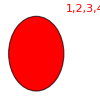
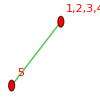
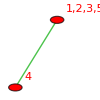
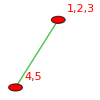
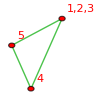
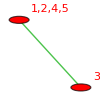
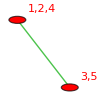
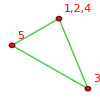
{-Graphics-{59048→v12345,1/6},-Graphics-{58288→v1234x5,1/2},-Graphics-{56770→v1235x4,1/2},-Graphics-{56012→v123x45,1/2},-Graphics-{56011→v123x4x5,1},-Graphics-{52232→v1245x3,1/2},-Graphics-{51478→v124x35,1/2},-Graphics-{51475→v124x3x5,1},-Graphics-{49972→v125x34,1/2},-Graphics-{49963→v125x3x4,1},-Graphics-{49220→v12x345,1/2},-Graphics-{49216→v12x34x5,1},-Graphics-{49210→v12x35x4,1},-Graphics-{49208→v12x3x45,1},-Graphics-{49207→v12x3x4x5,1},-Graphics-{39014→v1345x2,1/2},-Graphics-{38308→v134x25,1/2},-Graphics-{38281→v134x2x5,1},-Graphics-{36898→v135x24,1/2},-Graphics-{36817→v135x2x4,1},-Graphics-{36194→v13x245,1/2},-Graphics-{36166→v13x24x5,1},-Graphics-{36112→v13x25x4,1},-Graphics-{36086→v13x2x45,1},-Graphics-{36085→v13x2x4x5,1},-Graphics-{32684→v145x23,1/2},-Graphics-{32441→v145x2x3,1},-Graphics-{31984→v14x235,1/2},-Graphics-{31954→v14x23x5,1},-Graphics-{31738→v14x25x3,1},-Graphics-{31714→v14x2x35,1},-Graphics-{31711→v14x2x3x5,1},-Graphics-{30586→v15x234,1/2},-Graphics-{30496→v15x23x4,1},-Graphics-{30334→v15x24x3,1},-Graphics-{30262→v15x2x34,1},-Graphics-{30253→v15x2x3x4,1},-Graphics-{29888→v1x2345,1/2},-Graphics-{29857→v1x234x5,1},-Graphics-{29797→v1x235x4,1},-Graphics-{29768→v1x23x45,1},-Graphics-{29767→v1x23x4x5,1},-Graphics-{29633→v1x245x3,1},-Graphics-{29608→v1x24x35,1},-Graphics-{29605→v1x24x3x5,1},-Graphics-{29560→v1x25x34,1},-Graphics-{29551→v1x25x3x4,1},-Graphics-{29537→v1x2x345,1},-Graphics-{29533→v1x2x34x5,1},-Graphics-{29527→v1x2x35x4,1},-Graphics-{29525→v1x2x3x45,1},-Graphics-{29524→v1x2x3x4x5,0}}

```mathematica
Table[CosyPrint5[k],{k,baseKeys5}]
```

## We now replace some of the "b" variables with our greek letters

```mathematica
stubbornForm5=withComp5;
```

```mathematica
Keys[stubbornForm5[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,colortable,colofour,colortable2,comp,marked,parents,children,compwhy}

```mathematica
stubbornKeys5 = Select[Keys[stubbornForm5],(ToString[stubbornForm5[#]["comp"]]=="GreaterEqual")&];Length[stubbornKeys5]
```

125

```mathematica
Intersection[baseKeys5,stubbornKeys5]//Length
```

25

```mathematica
135
```

135

```mathematica
CosyPrintThree5[key_]:=ColorTablePrint[key,stubbornForm5,"colofour","colortable"]
```

```mathematica
ineqsthree5=Monitor[Table[stubbornForm5[k]["comp"][stubbornForm5[k]["colofour"],0],{k,Keys[stubbornForm5]}],k]//DeleteDuplicates;
```

```mathematica
Length[ineqsthree5]
```

1895

```mathematica
ineqsthree52=Fold[And,ineqsthree5]//Simplify
```

v12345>0&&v1234x5>0&&v1235x4>0&&v123x45>0&&v123x4x5>0&&v1245x3>0&&v124x35≥0&&v124x3x5≥0&&v125x34>0&&v125x3x4>0&&v12x345>0&&v12x34x5>0&&v12x35x4≥0&&v12x3x45>0&&v12x3x4x5>0&&v1345x2>0&&v134x25≥0&&v134x2x5≥0&&v135x24≥0&&v135x2x4≥0&&v13x245≥0&&v13x24x5≥0&&v13x25x4≥0&&v13x2x45≥0&&v13x2x4x5≥0&&v145x23>0&&v145x2x3>0&&v14x235≥0&&v14x23x5≥0&&v14x25x3≥0&&v14x2x35≥0&&v14x2x3x5≥0&&v15x234>0&&v15x23x4>0&&v15x24x3≥0&&v15x2x34>0&&v15x2x3x4>0&&v1x2345>0&&v1x234x5>0&&v1x235x4≥0&&v1x23x45>0&&v1x23x4x5>0&&v1x245x3≥0&&v1x24x35≥0&&v1x24x3x5≥0&&v1x25x34≥0&&v1x25x3x4≥0&&v1x2x345>0&&v1x2x34x5>0&&v1x2x35x4≥0&&v1x2x3x45>0&&v1x2x3x4x5==0&&v13x24x5+v13x2x4x5+v14x2x3x5+v1x24x3x5+v1x2x3x4x5>0&&v13x2x4x5+v14x2x35+v14x2x3x5+v1x2x35x4+v1x2x3x4x5>0&&v13x25x4+v14x25x3+v1x25x3x4>0&&v134x25+v1x25x34>0&&v13x25x4+v13x2x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5>0&&v13x24x5+v1x24x35+v1x24x3x5>0&&v13x245+v1x245x3>0&&v135x24+v15x24x3>0&&v14x25x3+v14x2x3x5+v1x24x3x5+v1x25x3x4+v1x2x3x4x5>0&&v14x2x35+v1x24x35+v1x2x35x4>0&&v14x235+v1x235x4>0&&v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5>0&&v14x25x3+v14x2x35+v14x2x3x5>0&&v14x235+v14x23x5>0&&v13x24x5+v13x25x4+v13x2x4x5>0&&v13x245+v13x2x45>0&&v135x24+v135x2x4>0&&v134x25+v134x2x5>0&&v124x35+v12x35x4>0&&v124x35+v124x3x5>0

```mathematica
ExpressionToTable[ineqsthree52]
```

v15x234>0
v14x235≥0
v13x245≥0
v145x2x3>0
v135x2x4≥0
v134x2x5≥0
v1x2x345>0
v1x2345>0
v12x345>0
v12345>0
v1x25x3x4≥0
v15x2x3x4>0
v15x23x4>0
v125x3x4>0
v1x24x3x5≥0
v14x2x3x5≥0
v14x23x5≥0
v124x3x5≥0
v15x24x3≥0
v13x2x4x5≥0
v13x24x5≥0
v1x2x34x5>0
v1x23x4x5>0
v1x234x5>0
v12x3x4x5>0
v12x34x5>0
v123x4x5>0
v1234x5>0
v1x2x3x4x5==0
v1345x2>0
v1x245x3≥0
v14x25x3≥0
v1245x3>0
v1x2x35x4≥0
v1x235x4≥0
v13x25x4≥0
v12x35x4≥0
v1235x4>0
v145x23>0
v135x24≥0
v134x25≥0
v1x25x34≥0
v15x2x34>0
v125x34>0
v1x24x35≥0
v14x2x35≥0
v124x35≥0
v13x2x45≥0
v1x2x3x45>0
v1x23x45>0
v12x3x45>0
v123x45>0
v14x235+v14x23x5>0
v14x235+v1x235x4>0
v13x245+v1x245x3>0
v13x245+v13x2x45>0
v135x24+v135x2x4>0
v134x25+v134x2x5>0
v124x35+v124x3x5>0
v135x24+v15x24x3>0
v124x35+v12x35x4>0
v134x25+v1x25x34>0
v13x25x4+v14x25x3+v1x25x3x4>0
v13x24x5+v1x24x35+v1x24x3x5>0
v14x25x3+v14x2x35+v14x2x3x5>0
v13x24x5+v13x25x4+v13x2x4x5>0
v14x2x35+v1x24x35+v1x2x35x4>0
v14x25x3+v14x2x3x5+v1x24x3x5+v1x25x3x4+v1x2x3x4x5>0
v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5>0
v13x25x4+v13x2x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5>0
v13x24x5+v13x2x4x5+v14x2x3x5+v1x24x3x5+v1x2x3x4x5>0
v13x2x4x5+v14x2x35+v14x2x3x5+v1x2x35x4+v1x2x3x4x5>0

```mathematica
baseGraphics5Rep=Map[stubbornForm5[#,"colofour"]->Labeled[Graph[stubbornForm5[#,"graph"],EdgeStyle->
If[ToString[stubbornForm5[#,"comp"]]=="Greater",Darker[Green],
If[ToString[stubbornForm5[#,"comp"]]=="Equal",
Blue,Red]]],stubbornForm5[#,"comp"]]&,baseKeys5]
```

{v12345→-Graphics-Greater,v1234x5→-Graphics-Greater,v1235x4→-Graphics-Greater,v123x45→-Graphics-Greater,v123x4x5→-Graphics-Greater,v1245x3→-Graphics-Greater,v124x35→-Graphics-GreaterEqual,v124x3x5→-Graphics-GreaterEqual,v125x34→-Graphics-Greater,v125x3x4→-Graphics-Greater,v12x345→-Graphics-Greater,v12x34x5→-Graphics-Greater,v12x35x4→-Graphics-GreaterEqual,v12x3x45→-Graphics-Greater,v12x3x4x5→-Graphics-Greater,v1345x2→-Graphics-Greater,v134x25→-Graphics-GreaterEqual,v134x2x5→-Graphics-GreaterEqual,v135x24→-Graphics-GreaterEqual,v135x2x4→-Graphics-GreaterEqual,v13x245→-Graphics-GreaterEqual,v13x24x5→-Graphics-GreaterEqual,v13x25x4→-Graphics-GreaterEqual,v13x2x45→-Graphics-GreaterEqual,v13x2x4x5→-Graphics-GreaterEqual,v145x23→-Graphics-Greater,v145x2x3→-Graphics-Greater,v14x235→-Graphics-GreaterEqual,v14x23x5→-Graphics-GreaterEqual,v14x25x3→-Graphics-GreaterEqual,v14x2x35→-Graphics-GreaterEqual,v14x2x3x5→-Graphics-GreaterEqual,v15x234→-Graphics-Greater,v15x23x4→-Graphics-Greater,v15x24x3→-Graphics-GreaterEqual,v15x2x34→-Graphics-Greater,v15x2x3x4→-Graphics-Greater,v1x2345→-Graphics-Greater,v1x234x5→-Graphics-Greater,v1x235x4→-Graphics-GreaterEqual,v1x23x45→-Graphics-Greater,v1x23x4x5→-Graphics-Greater,v1x245x3→-Graphics-GreaterEqual,v1x24x35→-Graphics-GreaterEqual,v1x24x3x5→-Graphics-GreaterEqual,v1x25x34→-Graphics-GreaterEqual,v1x25x3x4→-Graphics-GreaterEqual,v1x2x345→-Graphics-Greater,v1x2x34x5→-Graphics-Greater,v1x2x35x4→-Graphics-GreaterEqual,v1x2x3x45→-Graphics-Greater,v1x2x3x4x5→-Graphics-Equal}

```mathematica
(v14x25x35+v14x25x35+v2x3x5x5x14+v2x5x14x35+v2x5x14x35+v3x5x14x25+v3x5x14x25)+(v13x25x45+v14x25x35+v1x3x25x45+v1x3x4x5x25+v1x4x25x35+v3x5x14x25+v4x5x13x25)
```

v13x25x45+3 v14x25x35+v1x3x25x45+v1x3x4x5x25+v1x4x25x35+v2x3x5x5x14+2 v2x5x14x35+3 v3x5x14x25+v4x5x13x25

```mathematica
v13x25x45+2 v14x25x35+v14x25x35+v1x3x25x45+v1x3x4x5x25+v1x4x25x35+v2x3x5x5x14+v2x5x14x35+v2x5x14x35+v3x5x14x25+2 v3x5x14x25+v4x5x13x25
```

v13x25x45+3 v14x25x35+v1x3x25x45+v1x3x4x5x25+v1x4x25x35+v2x3x5x5x14+2 v2x5x14x35+3 v3x5x14x25+v4x5x13x25

## Now we look at the wheel with 5 outer vertices

```mathematica
wheel5colofour=2*stubbornForm5[empty5,"colofour"]-(stubbornForm5[threeDiagFrom1,"colofour"]+stubbornForm5[threeDiagFrom2,"colofour"]+stubbornForm5[twoDiagFrom3,"colofour"]+stubbornForm5[oneDiagFrom4,"colofour"])/.baseSimplify5Rep//Simplify
```

ReplaceAll::reps: {baseSimplify5Rep} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

2 Missing[KeyAbsent,empty5]-4 Missing[KeyAbsent,First[{}]]/.baseSimplify5Rep

```mathematica
2 v135x245+v135x24x5+v135x25x4+v135x2x45+v13x245x5+v13x25x45+v14x25x35+v14x25x35+v15x245x3+v15x24x35+v1x245x35
```

2 v135x245+v135x24x5+v135x25x4+v135x2x45+v13x245x5+v13x25x45+2 v14x25x35+v15x245x3+v15x24x35+v1x245x35

```mathematica
stubbornForm5[lambdaKey]
```

<|signature→20665,matrix→{{2,1,0,0,1},{1,2,1,0,0},{0,1,2,1,0},{0,0,1,2,1},{1,0,0,1,2}},graph→-Graphics-,vertexsets→{{1},{2},{3},{4},{5}},vertices→{1,2,3,4,5},edges→{{1,2},{1,5},{2,3},{3,4},{4,5}},relations→{x20665==-x46936+x982,x20665==x27226+x35977,x20665==x22852+x31681,x20665==x19936-x23608,x20665==x20422-x27550,x20665==x20746+x23041,x20665==x20692+x20803,x20665==x20656-x20758,x20665==x20668+x27259,x20665==x20664-x22856},links→{35977,27226,31681,22852,23041,20746,20803,20692,27259,20668},colortable→{{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v13x24x5+v13x25x4+v13x2x4x5,v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v14x25x3+v14x2x35+v14x2x3x5,v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v13x24x5+v1x24x35+v1x24x3x5,v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v13x25x4+v14x25x3+v1x25x3x4,v13x24x5+v13x2x4x5+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v14x2x35+v1x24x35+v1x2x35x4,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x3x5+v1x24x3x5+v1x25x3x4+v1x2x3x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5}},colofour→v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,colortable2→{{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v13x24x5+v13x25x4+v13x2x4x5,v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v14x25x3+v14x2x35+v14x2x3x5,v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v13x24x5+v1x24x35+v1x24x3x5,v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v13x25x4+v14x25x3+v1x25x3x4,v13x24x5+v13x2x4x5+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v14x2x35+v1x24x35+v1x2x35x4,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x3x5+v1x24x3x5+v1x25x3x4+v1x2x3x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5}},comp→Greater,marked→True,parents→{20664,20656,20422,19936,982},children→{{27226,35977},{22852,31681},{20746,23041},{20692,20803},{20668,27259}},compwhy→Embedding is planar and follows IH|>

```mathematica
Define some of graphs that have additional nodes
```

additional Define graphs have nodes of some that

```mathematica
sixNodes=stubbornForm5;
```

```mathematica
DefineFull[]:=Block[{empty = sixNodes[lambdaKey],amigo1=sixNodes[double1Key], amigo2=sixNodes[double5Key],amigo3=sixNodes[single24Key], newEntry},
newEntry=Association[];
newEntry["signature"]="full";
Table[
newEntry[key]=Simplify[2*empty[key]-(amigo1[key]+amigo2[key]+amigo3[key])]
,{key,{"colofour","colortable"}}
];
newEntry["comp"]=GreaterEqual;
newEntry["matrix"]=empty["matrix"];
newEntry["graph"]=Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->6,3<->6,4<->6,5<->6},VertexLabels->"Name",VertexSize->Normal,
ImageSize->{50,50},VertexCoordinates->sixPositions];
newEntry["vertexsets"]=empty["vertexsets"];
newEntry["vertices"]=empty["vertices"];
newEntry["relations"]={};
newEntry
]
```

```mathematica
DefineFull[]["graph"]
```

-Graphics-

```mathematica
sixNodes["full"]=DefineFull[];
```

```mathematica
1 spike missing
```

missing spike

```mathematica
sixNodes["B18"]=DefineNew["B18",double1Key,"full",EdgeDelete[sixNodes["full","graph"],{1<->6}]];
sixNodes["B19"]=DefineNew["B19",double2Key,"full",EdgeDelete[sixNodes["full","graph"],{2<->6}]];
sixNodes["B20"]=DefineNew["B20",double3Key,"full",EdgeDelete[sixNodes["full","graph"],{3<->6}]];
sixNodes["B21"]=DefineNew["B21",double4Key,"full",EdgeDelete[sixNodes["full","graph"],{4<->6}]];
sixNodes["B22"]=DefineNew["B22",double5Key,"full",EdgeDelete[sixNodes["full","graph"],{5<->6}]];
```

```mathematica
2 spikes missing
```

2 missing spikes

```mathematica
sixNodes["B23"]=DefineNew["B23","full","B18",EdgeDelete[sixNodes["B18","graph"],{2<->6}]];
sixNodes["B24"]=DefineNew["B24","full","B19",EdgeDelete[sixNodes["B19","graph"],{3<->6}]];
sixNodes["B25"]=DefineNew["B25","full","B20",EdgeDelete[sixNodes["B20","graph"],{4<->6}]];
sixNodes["B26"]=DefineNew["B26","full","B21",EdgeDelete[sixNodes["B21","graph"],{5<->6}]];
sixNodes["B27"]=DefineNew["B27","full","B22",EdgeDelete[sixNodes["B22","graph"],{1<->6}]];
```

```mathematica
Full with one spike in other direction
```

direction Full in one other spike with

```mathematica
sixNodes["B43"]=DefineNew["B43","B18",deltaKey,EdgeAdd[sixNodes["B18","graph"],{2<->5}],Subtract];
(*sixNodes["B43","comp"]=Greater;sixNodes["B43","compwhy"]="Obvious from colofour";*)
sixNodes["B44"]=DefineNew["B44","B19",alfaKey,EdgeAdd[sixNodes["B19","graph"],{1<->3}],Subtract];
(*sixNodes["B44","comp"]=Greater;sixNodes["B44","compwhy"]="Obvious from colofour";*)
sixNodes["B45"]=DefineNew["B45","B20",gammaKey,EdgeAdd[sixNodes["B20","graph"],{2<->4}],Subtract];
(*sixNodes["B45","comp"]=Greater;sixNodes["B45","compwhy"]="Obvious from colofour";*)
sixNodes["B46"]=DefineNew["B46","B21",epsilonKey,EdgeAdd[sixNodes["B21","graph"],{3<->5}],Subtract];
(*sixNodes["B46","comp"]=Greater;sixNodes["B46","compwhy"]="Obvious from colofour";*)
sixNodes["B47"]=DefineNew["B47","B22",betaKey,EdgeAdd[sixNodes["B22","graph"],{1<->4}],Subtract];
(*sixNodes["B47","comp"]=Greater;sixNodes["B47","compwhy"]="Obvious from colofour";*)
```

```mathematica
sixNodes["B47"]
```

<|signature→B47,colofour→2 v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5,colortable→{{0,2 v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5},{2 v13x24x5+v13x25x4+v13x2x4x5,v1x24x35+v1x24x3x5},{0,2 v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5},{0,2 v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5},{0,2 v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5},{2 v13x24x5+v1x24x35+v1x24x3x5,v13x25x4+v13x2x4x5},{v13x25x4,2 v13x24x5+v13x2x4x5+v1x24x35+v1x24x3x5},{0,2 v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5},{v1x24x35,2 v13x24x5+v13x25x4+v13x2x4x5+v1x24x3x5},{0,2 v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5}},colortable2→{{Missing[KeyAbsent,colortable2],v13x24x5+v13x2x4x5-v14x25x3-v14x2x35+v1x24x3x5+v1x2x3x4x5+Missing[KeyAbsent,colortable2]},{v13x24x5+v13x2x4x5+Missing[KeyAbsent,colortable2],-v14x25x3-v14x2x35+v1x24x3x5+v1x2x3x4x5+Missing[KeyAbsent,colortable2]},{-v14x25x3-v14x2x35+Missing[KeyAbsent,colortable2],v13x24x5+v13x2x4x5+v1x24x3x5+v1x2x3x4x5+Missing[KeyAbsent,colortable2]},{Missing[KeyAbsent,colortable2],v13x24x5+v13x2x4x5-v14x25x3-v14x2x35+v1x24x3x5+v1x2x3x4x5+Missing[KeyAbsent,colortable2]},{Missing[KeyAbsent,colortable2],v13x24x5+v13x2x4x5-v14x25x3-v14x2x35+v1x24x3x5+v1x2x3x4x5+Missing[KeyAbsent,colortable2]},{v13x24x5+v1x24x3x5+Missing[KeyAbsent,colortable2],v13x2x4x5-v14x25x3-v14x2x35+v1x2x3x4x5+Missing[KeyAbsent,colortable2]},{-v14x25x3+Missing[KeyAbsent,colortable2],v13x24x5+v13x2x4x5-v14x2x35+v1x24x3x5+v1x2x3x4x5+Missing[KeyAbsent,colortable2]},{Missing[KeyAbsent,colortable2],v13x24x5+v13x2x4x5-v14x25x3-v14x2x35+v1x24x3x5+v1x2x3x4x5+Missing[KeyAbsent,colortable2]},{-v14x2x35+Missing[KeyAbsent,colortable2],v13x24x5+v13x2x4x5-v14x25x3+v1x24x3x5+v1x2x3x4x5+Missing[KeyAbsent,colortable2]},{Missing[KeyAbsent,colortable2],v13x24x5+v13x2x4x5-v14x25x3-v14x2x35+v1x24x3x5+v1x2x3x4x5+Missing[KeyAbsent,colortable2]}},colofour2→Missing[KeyAbsent,colofour2],colortable3→Missing[KeyAbsent,colortable3],colofour3→Missing[KeyAbsent,colofour3],colortable4→Missing[KeyAbsent,colortable4],comp→GreaterEqual,relations→{xB47==-x31681+xB22},graph→-Graphics-|>

```mathematica
GetCompSix[key_]:=Block[{},sixNodes[key]]
```

```mathematica
SetCompSix[key_,value_]:=Block[{},sixNodes[key]=value]
```

```mathematica
CompGraph[getter_,key_]:=Labeled[Framed[Labeled[getter[key]["graph"],{Style[getter[key]["comp"],If[ToString[getter[key]["comp"]]=="Greater",Green,Red]],key},{Bottom,Top}]] ,key]
```

```mathematica
CompGraph[getter_,key_,colof_]:=Labeled[Framed[Labeled[getter[key]["graph"],{Style[getter[key]["comp"],If[ToString[getter[key]["comp"]]=="Greater",Green,Red]],getter[key][colof]},{Bottom,Top}]] ,key]
```

```mathematica
CheckCompFromRelations[getter_,setter_,key_]:=Block[{current=getter[key],rel2, lhs, rhs,one,two,three,onecomp,twocomp,threecomp, why,hold},
Table[
rel2=Simplify[rel];
lhs=rel2[[1]];
rhs=rel2[[2]];
If[Length[lhs]==0,
one=SymbolToKey[lhs];
two=SymbolToKey[rhs[[1]]];
three=SymbolToKey[rhs[[2]]];
,
one=SymbolToKey[rhs];
two=SymbolToKey[lhs[[1]]];
three=SymbolToKey[lhs[[2]]]
];
onecomp=ToString[getter[one]["comp"]];
twocomp=ToString[getter[two]["comp"]];
threecomp=ToString[getter[three]["comp"]];
If[onecomp=="GreaterEqual",
If[(twocomp=="Greater" )||( threecomp=="Greater"),
why="the relation holds : " <> ToString[rel2];
If[twocomp=="Greater",why=why <> " and x" <> ToString[two]<> " has a strictly positive colofour"];
If[threecomp=="Greater",why=why <> " and x" <> ToString[three]<> " has a strictly positive colofour"];
Print[{one,two,three,rel2,why,CompGraph[getter,one]==CompGraph[getter,two]+ CompGraph[getter,three]}];
hold=getter[one];
hold["compwhy"]=why;
hold["comp"]=Greater;
setter[one,hold];
1,
0
],
0
]
,{rel,current["relations"]}
]//Flatten
]
```

```mathematica
PropagateComp[getter_,setter_,keyset_:Keys[sixNodes]]:=Monitor[Flatten[Table[CheckCompFromRelations[getter,setter,key],{key,keyset}]],key]//Total
```

```mathematica
PropagateComp[GetCompSix,SetCompSix,Keys[sixNodes]]
```

{B18,29413,full,x29413+xfull==xB18,the relation holds : x29413 + xfull == xB18 and x29413 has a strictly positive colofour,-Graphics-GreaterEqualB18==-Graphics-Greater29413+-Graphics-GreaterEqualfull}

{B19,20773,full,x20773+xfull==xB19,the relation holds : x20773 + xfull == xB19 and x20773 has a strictly positive colofour,-Graphics-GreaterEqualB19==-Graphics-Greater20773+-Graphics-GreaterEqualfull}

{B20,27229,full,x27229+xfull==xB20,the relation holds : x27229 + xfull == xB20 and x27229 has a strictly positive colofour,-Graphics-GreaterEqualB20==-Graphics-Greater27229+-Graphics-GreaterEqualfull}

{B21,22933,full,x22933+xfull==xB21,the relation holds : x22933 + xfull == xB21 and x22933 has a strictly positive colofour,-Graphics-GreaterEqualB21==-Graphics-Greater22933+-Graphics-GreaterEqualfull}

{B22,20695,full,x20695+xfull==xB22,the relation holds : x20695 + xfull == xB22 and x20695 has a strictly positive colofour,-Graphics-GreaterEqualB22==-Graphics-Greater20695+-Graphics-GreaterEqualfull}

{B23,B18,full,xB18+xfull==xB23,the relation holds : xB18 + xfull == xB23 and xB18 has a strictly positive colofour,-Graphics-GreaterEqualB23==-Graphics-GreaterB18+-Graphics-GreaterEqualfull}

{B24,B19,full,xB19+xfull==xB24,the relation holds : xB19 + xfull == xB24 and xB19 has a strictly positive colofour,-Graphics-GreaterEqualB24==-Graphics-GreaterB19+-Graphics-GreaterEqualfull}

{B25,B20,full,xB20+xfull==xB25,the relation holds : xB20 + xfull == xB25 and xB20 has a strictly positive colofour,-Graphics-GreaterEqualB25==-Graphics-GreaterB20+-Graphics-GreaterEqualfull}

{B26,B21,full,xB21+xfull==xB26,the relation holds : xB21 + xfull == xB26 and xB21 has a strictly positive colofour,-Graphics-GreaterEqualB26==-Graphics-GreaterB21+-Graphics-GreaterEqualfull}

{B27,B22,full,xB22+xfull==xB27,the relation holds : xB22 + xfull == xB27 and xB22 has a strictly positive colofour,-Graphics-GreaterEqualB27==-Graphics-GreaterB22+-Graphics-GreaterEqualfull}

```mathematica
PropagateComp[GetCompSix,SetCompSix,Keys[sixNodes]]
```

{B51,B18,B52,xB18+xB52==xB51,the relation holds : xB18 + xB52 == xB51 and xB18 has a strictly positive colofour,-Graphics-GreaterEqualB51B51==-Graphics-GreaterB18B18+-Graphics-GreaterEqualB52B52}

```mathematica
PropagateComp[GetCompSix,SetCompSix,Keys[sixNodes]]
```

0

```mathematica
Add a 7 th node
```

7 a Add node th

```mathematica
DefineB50[]:=Block[{base=sixNodes["B18"], newEntry},
newEntry=Association[];
newEntry["signature"]="B50";
Table[
newEntry[key]=Simplify[4*base[key]]
,{key,{"colofour","colortable"}}
];
newEntry["comp"]=base["comp"];
newEntry["matrix"]=base["matrix"];
newEntry["graph"]=VertexAdd[base["graph"],7];
newEntry["vertexsets"]=base["vertexsets"];
newEntry["vertices"]=base["vertices"];
newEntry["relations"]={};
newEntry
]
sixNodes["B50"]=DefineB50[];
sixNodes["B51"]=DefineNew["B51","B50","B18",EdgeAdd[sixNodes["B50","graph"],{1<->7}],Subtract];
sixNodes["B52"]=DefineNew["B52","B51","B18",EdgeAdd[sixNodes["B51","graph"],{2<->7}],Subtract];
sixNodes["B53"]=DefineNew["B53","B52","full",EdgeAdd[sixNodes["B52","graph"],{6<->7}],Subtract];
```

```mathematica
sixNodes["B54"]=DefineNew["B54","B53","B43",EdgeAdd[sixNodes["B53","graph"],{5<->7}],Subtract]
```

<|signature→B54,colofour→v13x25x4+v14x25x3+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5,colortable→{{0,v13x25x4+v14x25x3+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v13x25x4,v14x25x3+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v14x25x3,v13x25x4+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{0,v13x25x4+v14x25x3+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{0,v13x25x4+v14x25x3+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v1x24x35+v1x24x3x5,v13x25x4+v14x25x3+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v13x25x4+v14x25x3+2 v1x25x3x4,v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5},{0,v13x25x4+v14x25x3+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v1x24x35+v1x2x35x4,v13x25x4+v14x25x3+v1x24x3x5+2 v1x25x3x4+v1x2x3x4x5},{0,v13x25x4+v14x25x3+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5}},colortable2→{{-3 Missing[KeyAbsent,colortable2],v13x25x4+v14x25x3-3 v1x24x35-3 v1x24x3x5-2 v1x25x3x4-3 v1x2x35x4-3 v1x2x3x4x5-3 Missing[KeyAbsent,colortable2]},{v13x25x4-3 Missing[KeyAbsent,colortable2],v14x25x3-3 v1x24x35-3 v1x24x3x5-2 v1x25x3x4-3 v1x2x35x4-3 v1x2x3x4x5-3 Missing[KeyAbsent,colortable2]},{v14x25x3-3 Missing[KeyAbsent,colortable2],v13x25x4-3 v1x24x35-3 v1x24x3x5-2 v1x25x3x4-3 v1x2x35x4-3 v1x2x3x4x5-3 Missing[KeyAbsent,colortable2]},{-3 Missing[KeyAbsent,colortable2],v13x25x4+v14x25x3-3 v1x24x35-3 v1x24x3x5-2 v1x25x3x4-3 v1x2x35x4-3 v1x2x3x4x5-3 Missing[KeyAbsent,colortable2]},{-3 Missing[KeyAbsent,colortable2],v13x25x4+v14x25x3-3 v1x24x35-3 v1x24x3x5-2 v1x25x3x4-3 v1x2x35x4-3 v1x2x3x4x5-3 Missing[KeyAbsent,colortable2]},{-3 (v1x24x35+v1x24x3x5+Missing[KeyAbsent,colortable2]),v13x25x4+v14x25x3-2 v1x25x3x4-3 v1x2x35x4-3 v1x2x3x4x5-3 Missing[KeyAbsent,colortable2]},{v13x25x4+v14x25x3-2 v1x25x3x4-3 Missing[KeyAbsent,colortable2],-3 (v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5+Missing[KeyAbsent,colortable2])},{-3 Missing[KeyAbsent,colortable2],v13x25x4+v14x25x3-3 v1x24x35-3 v1x24x3x5-2 v1x25x3x4-3 v1x2x35x4-3 v1x2x3x4x5-3 Missing[KeyAbsent,colortable2]},{-3 (v1x24x35+v1x2x35x4+Missing[KeyAbsent,colortable2]),v13x25x4+v14x25x3-3 v1x24x3x5-2 v1x25x3x4-3 v1x2x3x4x5-3 Missing[KeyAbsent,colortable2]},{-3 Missing[KeyAbsent,colortable2],v13x25x4+v14x25x3-3 v1x24x35-3 v1x24x3x5-2 v1x25x3x4-3 v1x2x35x4-3 v1x2x3x4x5-3 Missing[KeyAbsent,colortable2]}},colofour2→-5 Missing[KeyAbsent,colofour2],colortable3→-5 Missing[KeyAbsent,colortable3],colofour3→-5 Missing[KeyAbsent,colofour3],colortable4→-5 Missing[KeyAbsent,colortable4],comp→GreaterEqual,relations→{xB54==-xB43+xB53},graph→-Graphics-|>

```mathematica
CompGraph[GetCompSix,"B54"]
```

-Graphics-GreaterEqualB54B54

```mathematica
InverseKey[colofour_]:=First[Select[Keys[sixNodes],sixNodes[#]["colofour"]==colofour&]]
```

```mathematica
Map[CompGraph[GetCompSix,InverseKey[#]]&,ListofVars[sixNodes["B54","colofour"]]]
```

{-Graphics-GreaterEqual3611236112,-Graphics-GreaterEqual3173831738,-Graphics-GreaterEqual2960829608,-Graphics-GreaterEqual2960529605,-Graphics-GreaterEqual2952729527,-Graphics-Equal2952429524,-Graphics-GreaterEqual2955129551}

```mathematica
CompGraph[GetCompSix,"B43"]
```

-Graphics-GreaterEqualB43B43

```mathematica
Map[{CompGraph[GetCompSix,InverseKey[#]],sixNodes[InverseKey[#],"comp"]}&,ListofVars[sixNodes["B43","colofour"]]]
```

{{-Graphics-GreaterEqual3616636166,GreaterEqual},{-Graphics-GreaterEqual3171431714,GreaterEqual},{-Graphics-GreaterEqual2960529605,GreaterEqual},{-Graphics-GreaterEqual2952729527,GreaterEqual},{-Graphics-GreaterEqual2960829608,GreaterEqual}}

```mathematica
sixNodes[36166]
```

<|signature→36166,matrix→{{2,1,2,1,1},{1,2,1,2,1},{2,1,2,1,1},{1,2,1,2,1},{1,1,1,1,2}},graph→-Graphics-,vertexsets→{{5},{1,3},{2,4}},vertices→{1,2,3},edges→{{1,2},{1,3},{2,3}},relations→{x36166==x35434-x36898,x36166==x36138-x36194,x36166==x14044-x58288},links→{},colofour→v13x24x5,colortable→{{0,v13x24x5},{v13x24x5,0},{0,v13x24x5},{0,v13x24x5},{0,v13x24x5},{v13x24x5,0},{0,v13x24x5},{0,v13x24x5},{0,v13x24x5},{0,v13x24x5}},colortable2→{{0,v13x24x5},{v13x24x5,0},{0,v13x24x5},{0,v13x24x5},{0,v13x24x5},{v13x24x5,0},{0,v13x24x5},{0,v13x24x5},{0,v13x24x5},{0,v13x24x5}},comp→GreaterEqual,marked→True,parents→{36138,35434,36004,33808,36003,33807,35977,33781,23044,23041,22792,22789,22315,22063,14044,16078,16077,16051,1174,1171,445},children→{}|>